## Circular motion example

### Define the unit vectors î and ĵ

```mathematica
iHat = {1,0}
```

{1,0}

```mathematica
jHat = {0,1}
```

{0,1}

Check that the dot products are as expected

```mathematica
iHat .jHat
```

0

```mathematica
iHat.iHat
```

1

```mathematica
Dot[iHat,iHat]
```

1

### Set up the problem geometry

Set a vector for the observer’s position

```mathematica
rObs = -c iHat
```

{-c,0}

Set a vector for the particle’s position

```mathematica
r[t_]=a Cos[ω t]iHat + (b + a Sin[ω t]) jHat
```

{a cos(t ω),a sin(t ω)+b}

Find the LOS vector p=r(t)-r_obs

```mathematica
p[t_]=r[t]-rObs
```

{a cos(t ω)+c,a sin(t ω)+b}

### Compute the particle’s velocity

```mathematica
v[t_]=r'[t]
```

{-a ω sin(t ω),a ω cos(t ω)}

### Find the LOS velocity

The component of v(t) along the LOS is v_LOS(t)= p̂(t)·v(t), where p̂(t) is the unit vector in the direction of the LOS vector p(t). To find p̂(t), normalize p(t) by dividing by its magnitude: p̂=p/(√(p·p)).

Compute p̂

```mathematica
pHat[t_]=p[t]/Sqrt[p[t].p[t]] // FullSimplify
```

{(a cos(t ω)+c)/(√((a sin(t ω)+b)^2+(a cos(t ω)+c)^2)),(a sin(t ω)+b)/(√((a sin(t ω)+b)^2+(a cos(t ω)+c)^2))}

Dot p̂  into velocity

```mathematica
vLOS[t_]=pHat[t].v[t]//FullSimplify
```

(a ω (b cos(t ω)-c sin(t ω)))/(√((a sin(t ω)+b)^2+(a cos(t ω)+c)^2))

```mathematica
v1[t_]=vLOS[t] /. {a->1/2,b->3/4,c->3/4,ω->1}
```

((3 cos(t))/4-(3 sin(t))/4)/(2 √(((sin(t))/2+3/4)^2+((cos(t))/2+3/4)^2))

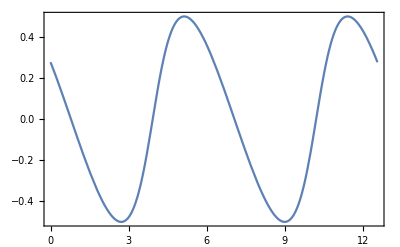

```mathematica
Plot[v1[t],{t,0,4Pi}]
```